# Laboratorio 2

## Definición de Sistema

```mathematica
ϕ[α_,β_,c_]:= α x^c+β y^c;
DinamicaBidimensional[α_,β_,c_]:= {α x^c-ϕ[α,β,c] x, β y^c-ϕ[α,β,c] y};
DinamicaUnidimensional[α_,β_,c_]:= α x^c(1-x) - β x(1-x)^c;
```

## Plano Fase

```mathematica
Jacobiano[M_,vars_]:=Outer[D,M,vars]/;Equal@@(Dimensions[#]&/@{M,vars})
```

```mathematica
PhasePlane[Dinamica_,vars_,Label_]:=Module[{P,J,Colors},
(*Puntos de equilibrio.*)
P=vars/.Quiet@Solve[Dinamica==0,vars,Reals];
(*Calculo de estabilidad a P. Azul estable y rojo inestable.*)
J=Jacobiano[Dinamica,vars];
Colors=If[VectorLess[{Eigenvalues@(J/.Thread[vars->#]),0}],Blue,Red]&/@P;
Show[
StreamPlot[Dinamica,{x,-1,2},{y,-1,2},PlotLabel->Label],

MapThread[Graphics[{PointSize[0.025],#1,Point[#2]}]&,{Colors,P}]
]
]
```

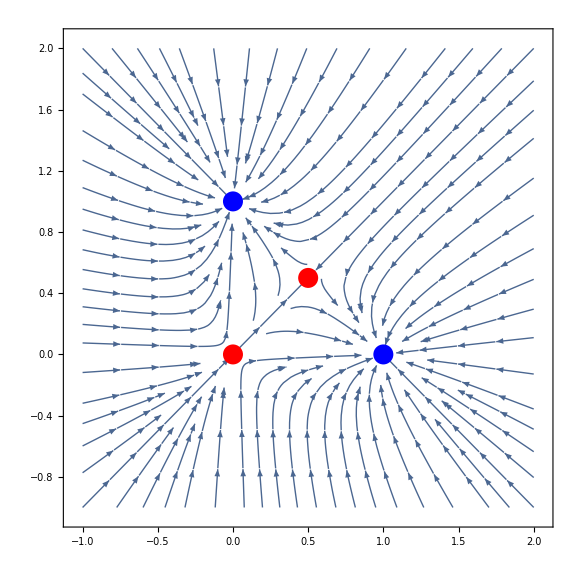

```mathematica
PhasePlane[DinamicaBidimensional[1,1,2],{x,y},None]
```

## Isoclinas

```mathematica
Isoclines[Dinamica_,var_,Label_]:=Module[{P,derivative,Colors},
(*Puntos de equilibrio.*)
P=var/.Quiet@Solve[Dinamica==0,var,Reals];
(*Calculo de estabilidad a P. Rojo inestable y azul estable.*)
derivative=D[Dinamica,var];
Colors=If[(derivative/.(var->#))<0,Blue,Red]&/@P;
Show[
StreamPlot[{1,Dinamica},{t,0,10},{x,-1,2}, PlotLabel->Label],
MapThread[Graphics[{Dashed,#1,Thick,Line[{{0,#2},{10,#2}}]}]&,{Colors,P}]
]
]
```

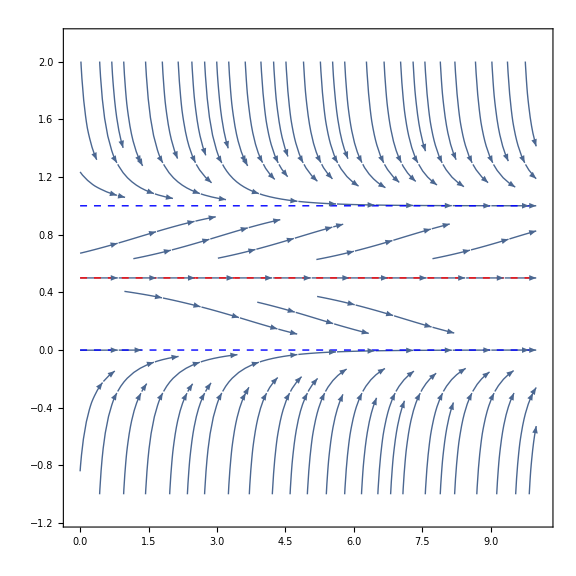

```mathematica
Isoclines[DinamicaUnidimensional[1,1,2],x,None]
```

## Explorador de Parámetros

```mathematica
Manipulate[Clear[#] & /@ {x, y};
   MyLabel = "c = " <> ToString[c] <> ", α = " <> ToString[α] <> ", β = " <> ToString[β];
   {PhasePlane[DinamicaBidimensional[α, β, c], {x, y}, MyLabel], Isoclines[DinamicaUnidimensional[α, β, c], x, None]} // GraphicsRow,
   {{α, 1}, -5, 5}, {{β, 1}, -5, 5}, {{c, 2}, -3, 3, 1}
]
```

## Interpretación

Debido a la simetría de las ecuaciones, es suficiente el análisis de una de las ecuaciones. 

Se puede reescribir la ecuación de la forma:

ⅆx/ⅆt=αx^c(1-x)-(βx(1-x))^c

En donde se disciernen claramente los términos no-negativos de crecimiento y de decrecimiento.
Además recordando que la población total esta normalizada:


ⅆx/ⅆt=αx^c y-βxy^c

En esta forma se le puede dar la siguiente interpretación. Dinámica de población de lobos y 
humanos, los lobos necesitan atacar en manadas de al menos c individuos a un humano para
comerselo y viceversa. Los parámetros α y β representan la probabilidad de ocurrencia de dicho
evento. El problema de esta interpretación es que requiere una dinámica discreta sin embargo es 
una aproximación continua.

Se encontraron empíricamente dos parámetros de bifurcación: 0 y 1. A continuación se analizará 
caso por caso.

Si c es mayor que uno entonces la interpretación dada funciona, teniendo como puntos de equilibrio 
cuando no hay población (inestable), cuando toda la población es x (estable), cuando toda es y 
(estable) y por último lo mas interesante es cuando la población x se come tantos individuos y 
como y se comen de x. En el diagrama se puede observar un equilibrio sobre la recta definida por 
los puntos ((0,1),(1,0)) en α/(α+β). Cabe notar que este último equilibrio es inestable porque 
si hay una mayoría de cualquier tipo se volvera dominante. 

Cuando c es uno podemos escribir la ecuación como:

ⅆx/ⅆt=(α-β)xy

Entonces se observa que no pueden coexistir las especies y el último punto de equilibrio del caso 
anterior desaparece.

Si c esta en el intervalo unitario el término de crecimiento de una especie esta dominado por la
población de la otra especie y no de la propia. En este caso una interpretación mas apropiada 
podría ser un fenómeno de cooperación. Los puntos de equilibrio en donde solo hay una especie se 
vuelven inestables debido a que la especie aporta mas a su decrecimiento que a su crecimiento. Las 
especies tienen que convivir para sobrevivir por lo tanto el único punto de equilibrio estable del 
sistema es en α/(α+β).

En el caso donde c es nulo, no tiene sentido claro mi interpretación debido a que es posible cazar
lobos sin que haya lobos y viceversa. En este caso el único punto de equilibrio estable es el de 
convivencia. De manera muy similar cuando c es menor a cero la especie es mala para si misma y 
por lo tanto su única opción para sobrevivir es con la ayuda de la otra especie. Esto impone una 
dinámica similar al caso donde c es nulo pero con trayectorias distorsionadas.